High order Ne.b4de.b4lec elements with local complete sequence properties
	Joachim Scho.a8berl and Sabine Zaglmayr

```mathematica
Needs["VectorAnalysis`"]
SetCoordinates[Cartesian[x,y,z]];
```

the Legendrepolynomials       l_i(x)  (i=0,...p)
	l_i(x):=ix

```mathematica
l(i_,x_):=ix;
```

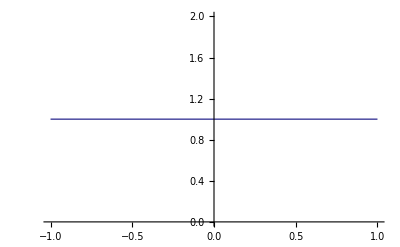
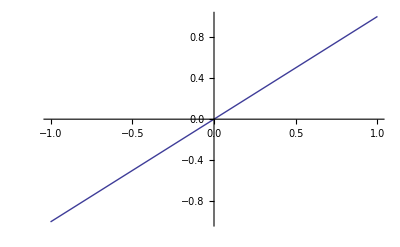
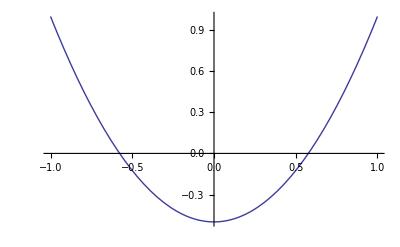
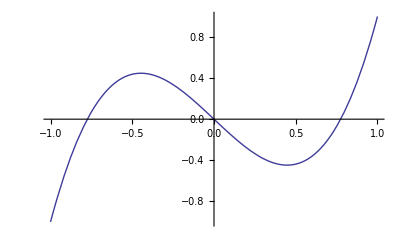
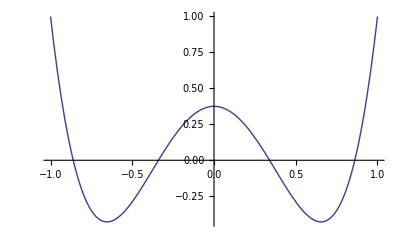
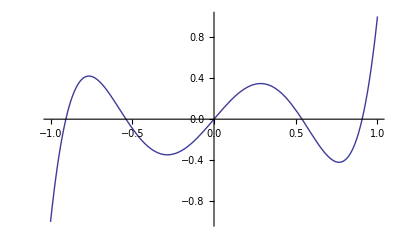

```mathematica
Table[Plot[l[i, x], {x,-1,1}], {i,0,5}]
```

theintegratedLegendre-polynomialsL_i(i=2,...,p)
L_i_[x_]:=∫_-1^x i-1zⅆz

```mathematica
L(i_,x_):=∫_-1^x l(i-1,z)ⅆz
```

```mathematica
For[i=2,i≤6,i++,    L(i,x_)=∫_-1^x l(i-1,z)ⅆz     ]
```

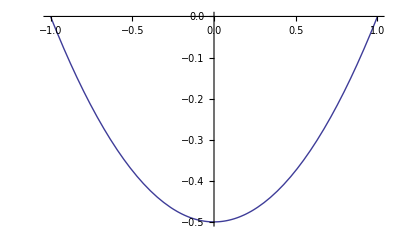
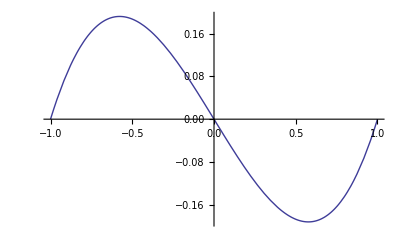
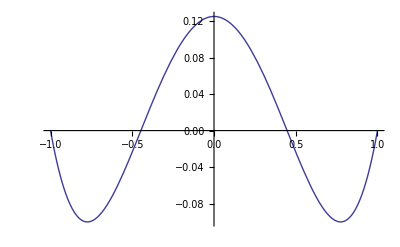
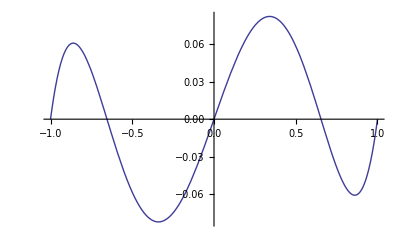

```mathematica
Table[Plot[L(i,x),{x,-1,1}],{i,2,5}]
```

the scaled Legendre polynomials

```mathematica
lS(n_,s_,t_):=Simplify[t^n l(n,s/t)];
```

```mathematica
Table[Plot3D[lS[i,s,t],{s,-1,1},{t,0,1},RegionFunction->Function[{s,t,z},0>s-t && 0<s+t]],
{i,0,3}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

the scaled integrated Legendre polynomials

```mathematica
LS(n_,s_,t_):=Simplify[t^n L(n,s/t)];
```

```mathematica
Table[Plot3D[LS[i,s,t],{s,-1,1},{t,0,1},RegionFunction->Function[{s,t,z},0>s-t && 0<s+t]],
{i,2,5}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

the barycentric coordinates
	λ_i (i=1,2,3,4)

```mathematica
Clear[point, lamda,px, edge,face]
point[0]={0,0,0};  point[1]={1,0,0}; point[2]={0,1,0}; point[3]={0,0,1};
edge[0]={0,1}; edge[1]={0,2};edge[2]={0,3}; edge[3]={1,2}; edge[4]={1,3}; edge[5]={2,3};
face[0]={0,1,2}; face[1]={0,1,3};face[2]={0,2,3};face[3]={1,2,3};

px={0,0,0};
For[i=0,i<4, ++i, px+=point[i]*lamda[i];]
sum=0;
For[i=0,i<4, ++i, sum+=lamda[i]];
px=Append[px, sum];
sol=Solve[px=={x,y,z,1}, {lamda[0],lamda[1], lamda[2], lamda[3]}];
lamda[0]=lamda[0]/.sol[[1]];
lamda[1]=lamda[1]/.sol[[1]];
lamda[2]=lamda[2]/.sol[[1]];
lamda[3]=lamda[3]/.sol[[1]];
```

General::spell1: スペル間違いの可能性があります．新規シンボル"point"はすでにあるシンボル"Point"に似ています．

General::spell1: スペル間違いの可能性があります．新規シンボル"edge"はすでにあるシンボル"Wedge"に似ています．

General::spell1: スペル間違いの可能性があります．新規シンボル"sum"はすでにあるシンボル"Sum"に似ています．

```mathematica
Clear[lines];
lines={Thick};
For[i=0, i<6, i++,
p1= edge[i][[1]];
p2=edge[i][[2]];
line=Line[ { point[p1] ,point[ p2]  }  ] ;
lines=Append[lines, line];
]
Graphics3D[lines,Axes->True,AxesLabel->{x,y,z}, Boxed->True,ViewVertical->{0,0,1}]
```

General::spell: スペル間違いの可能性があります．新規シンボル"line"はすでにあるシンボル{Line, lines}に似ています．

-Graphics3D-

```mathematica
G[func_,fac0_]:=Module[{ncf, fac=fac0, cf},
ncf=16;
cf=Table[(-1+2/ncf*(i-1/2))*fac, {i,1,ncf} ];
 ContourPlot3D[func,{x,0,1},{y,0,1},{z,0,1},Contours->cf, RegionFunction->Function[{x,y,z}, lamda[0]>0], ColorFunction->ColorData["TemperatureMap"],
Mesh->None,ContourStyle->Directive[Opacity[0.5]]
 ] 
]
```

Hierarchical triangular H1- element  of order p using Scaled Legendre Polynomials

```mathematica
-Graphics-;
```

Vertex - based functions

```mathematica
phiV[i_]:=lamda[i];
```

Edge - based functions

```mathematica
phiE[m_,i_]:=LS[i, 
lamda[edge[m][[1]]]- lamda[edge[m][[2]]],
lamda[edge[m][[2]]]+ lamda[edge[m][[1]]] ];
```

General::spell1: スペル間違いの可能性があります．新規シンボル"phiE"はすでにあるシンボル"phiV"に似ています．

Face-based functions

```mathematica
u[f_, i_]:=LS[i+2, lamda[face[f][[1]]]- lamda[face[f][[2]]],lamda[face[f][[1]]]+ lamda[face[f][[2]]] ];
v[f_,j_]:= lamda[face[f][[3]]]*lS[j,lamda[face[f][[3]]]-lamda[face[f][[1]]]-lamda[face[f][[2]]],     lamda[face[f][[1]]]+lamda[face[f][[2]]]+lamda[face[f][[3]]] ] 
phiF[f_,i_,j_]:=u[f,i]*v[f,j];
```

General::spell: スペル間違いの可能性があります．新規シンボル"phiF"はすでにあるシンボル{phiE, phiV}に似ています．

Interir-based functions

```mathematica
uI[i_]:=LS[i+2, lamda[0]-lamda[1], lamda[0]+lamda[1] ];
vI[j_]:=lamda[2]*lS[j, lamda[2]-lamda[0]-lamda[1], lamda[0]+lamda[1]+lamda[2] ];
wI[k_]:=lamda[3] *l[k, lamda[3]-lamda[0]-lamda[1]-lamda[2] ];
phiI[i_,j_,k_]:=uI[i]*vI[j]*wI[k];
(*phiI[i_,j_,k_]:=LS[i+2, lamda[0]-lamda[1], lamda[0]+lamda[1] ]*lamda[2]*lS[j, lamda[2]-lamda[0]-lamda[1], lamda[0]+lamda[1]+lamda[2] ]*lamda[3] *l[k, lamda[3]-lamda[0]-lamda[1]-lamda[2] ];*)
```

General::spell: スペル間違いの可能性があります．新規シンボル"phiI"はすでにあるシンボル{phiE, phiF, phiV}に似ています．

p=1
Vertex - based functions

```mathematica
Table[G[phiV[i],1],{i,0,3}]
Table[phiV[i],{i,0,3}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

{1-x-y-z,x,y,z}

p=2
Edge - based functions

```mathematica
p=2;
Table[G[ phiE[e,p],1/2] ,{e,0,5}]
Table[phiE[e,p],{e,0,5}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

{2 x (-1+x+y+z),2 y (-1+x+y+z),2 z (-1+x+y+z),-2 x y,-2 x z,-2 y z}

p=3
Edge - based functions

```mathematica
p=3;
Table[G[phiE[m,p],1/4],{m,0,5}]
Factor[Table[phiE[m,p],{m,0,5}]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

{-2 x (-1+x+y+z) (-1+2 x+y+z),-2 y (-1+x+y+z) (-1+x+2 y+z),-2 z (-1+x+y+z) (-1+x+y+2 z),-2 x (x-y) y,-2 x (x-z) z,-2 y (y-z) z}

Face functions

```mathematica
p=3;
Table[G[phiF[f, i,p-3-i], 1/8],{i,0,p-3}, {f,0,3}]
Factor[Table[phiF[f ,i,p-3-i],{i,0,p-3}, {f,0,3}]]
```

{{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}}

{{2 x y (-1+x+y+z),2 x z (-1+x+y+z),2 y z (-1+x+y+z),-2 x y z}}

p=4
Edge - based functions

```mathematica
p=4;
Table[G[ phiE[e,p],1/8] ,{e,0,5}]
Factor[Table[phiE[e,p],{e,0,5}]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

{2 x (-1+x+y+z) (1-5 x+5 x^2-2 y+5 x y+y^2-2 z+5 x z+2 y z+z^2),2 y (-1+x+y+z) (1-2 x+x^2-5 y+5 x y+5 y^2-2 z+2 x z+5 y z+z^2),2 z (-1+x+y+z) (1-2 x+x^2-2 y+2 x y+y^2-5 z+5 x z+5 y z+5 z^2),-2 x y (x^2-3 x y+y^2),-2 x z (x^2-3 x z+z^2),-2 y z (y^2-3 y z+z^2)}

Face functions

```mathematica
p=4;
Table[G[phiF[f, i,p-3-i], 1/16],{i,0,p-3}, {f,0,3}]
Factor[Table[phiF[f ,i,p-3-i],{i,0,p-3}, {f,0,3}]]
```

{{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}}

{{2 x y (-1+x+y+z) (-1+2 y+z),2 x z (-1+x+y+z) (-1+y+2 z),2 y z (-1+x+y+z) (-1+x+2 z),2 x y (x+y-z) z},{-2 x y (-1+x+y+z) (-1+2 x+y+z),-2 x z (-1+x+y+z) (-1+2 x+y+z),-2 y z (-1+x+y+z) (-1+x+2 y+z),-2 x (x-y) y z}}

Interior-based functions

```mathematica
p=4;
Table[G[phiI[ 0,0,0], 1/64],{i,0,p-4}]
Factor[Table[phiI[0,0,0],{i,0,p-4} ]]
```

{-Graphics3D-}

{2 x y z (-1+x+y+z)}

p=5
Edge - based functions

```mathematica
p=5;
Table[G[ phiE[e,p],1/8] ,{e,0,5}]
Factor[Table[phiE[e,p],{e,0,5}]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

{-2 x (-1+x+y+z) (-1+2 x+y+z) (1-7 x+7 x^2-2 y+7 x y+y^2-2 z+7 x z+2 y z+z^2),-2 y (-1+x+y+z) (-1+x+2 y+z) (1-2 x+x^2-7 y+7 x y+7 y^2-2 z+2 x z+7 y z+z^2),-2 z (-1+x+y+z) (-1+x+y+2 z) (1-2 x+x^2-2 y+2 x y+y^2-7 z+7 x z+7 y z+7 z^2),-2 x (x-y) y (x^2-5 x y+y^2),-2 x (x-z) z (x^2-5 x z+z^2),-2 y (y-z) z (y^2-5 y z+z^2)}

Face functions

```mathematica
p=5;
Table[G[phiF[f, i,p-3-i], 1/32],{i,0,p-3}, {f,0,3}]
Factor[Table[phiF[f ,i,p-3-i],{i,0,p-3}, {f,0,3}]]
```

{{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}}

{{2 x y (-1+x+y+z) (1-6 y+6 y^2-2 z+6 y z+z^2),2 x z (-1+x+y+z) (1-2 y+y^2-6 z+6 y z+6 z^2),2 y z (-1+x+y+z) (1-2 x+x^2-6 z+6 x z+6 z^2),-2 x y z (x^2+2 x y+y^2-4 x z-4 y z+z^2)},{-2 x y (-1+x+y+z) (-1+2 x+y+z) (-1+2 y+z),-2 x z (-1+x+y+z) (-1+2 x+y+z) (-1+y+2 z),-2 y z (-1+x+y+z) (-1+x+2 y+z) (-1+x+2 z),2 x (x-y) y (x+y-z) z},{2 x y (-1+x+y+z) (1-5 x+5 x^2-2 y+5 x y+y^2-2 z+5 x z+2 y z+z^2),2 x z (-1+x+y+z) (1-5 x+5 x^2-2 y+5 x y+y^2-2 z+5 x z+2 y z+z^2),2 y z (-1+x+y+z) (1-2 x+x^2-5 y+5 x y+5 y^2-2 z+2 x z+5 y z+z^2),-2 x y (x^2-3 x y+y^2) z}}

Interior-based functions

```mathematica
p=5;
{G[phiI[ 1,0,0], 1/256],G[phiI[ 0,1,0], 1/256],G[phiI[ 0,0,1], 1/256] }
Factor[{phiI[1,0,0],phiI[0,1,0],phiI[0,0,1]}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

{-2 x y z (-1+x+y+z) (-1+2 x+y+z),2 x y z (-1+x+y+z) (-1+2 y+z),2 x y z (-1+x+y+z) (-1+2 z)}